```mathematica
Simplify@D[4ϵ((σ/r)^12-(σ/r)^6),r]
```

(24 ϵ σ^6 (r^6-2 σ^6))/r^13

-Graphics3D-

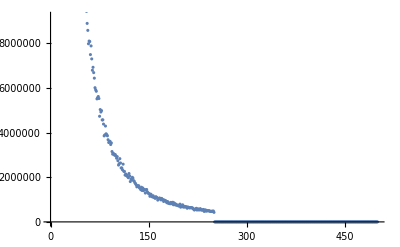

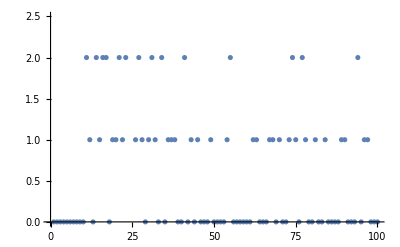

```mathematica
scaleFactor=10^9;
initPositions= ReadList["~/phd-stuff/courses/astrid_sim/positions.txt",Number,RecordLists->True]*scaleFactor;
ListPointPlot3D[initPositions,BoxRatios->{1, 1, 1},AxesLabel->{"x","y","z"}]
velocities= ReadList["~/phd-stuff/courses/astrid_sim/velocities.txt",Number,RecordLists->False];
sortvelocities=Sort[Flatten@velocities];
rdf= ReadList["~/phd-stuff/courses/astrid_sim/radialdistfunc.txt",Number,RecordLists->False];
ListPlot[rdf]
veldist = ReadList["~/phd-stuff/courses/astrid_sim/speeddist.txt",Number,RecordLists->False];
ListPlot[veldist]
```

```mathematica
Table[{k,initPositions[[k]]},{k,1,Length[initPositions]}];
numvel=Table[{k,velocities[[k]]},{k,1,Length[velocities]}];
Sort[numvel,#1[[2]]>#2[[2]]&];
```

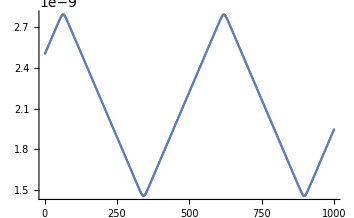

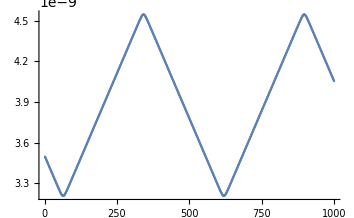

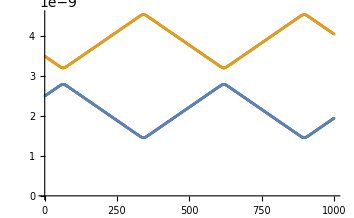

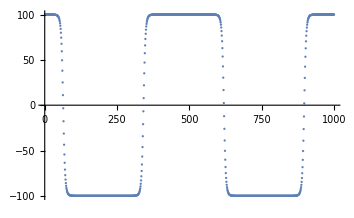

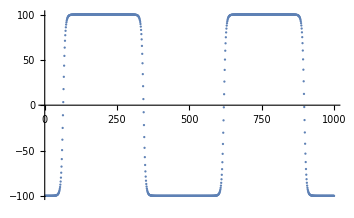

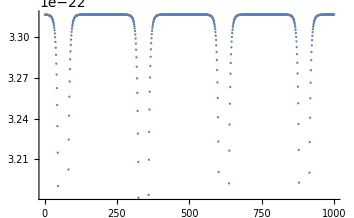

-Graphics-

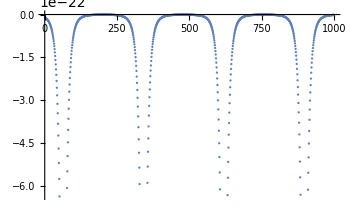

-Graphics-

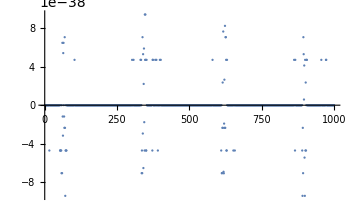

```mathematica
verlet= ReadList["~/phd-stuff/courses/astrid_sim/periodicverlet.txt",Number,RecordLists->True];

xpos=Table[verlet[[1+3*i]][[1]],{i,0,Length[(verlet)]/3-1}];
v=Table[verlet[[1+3*i]][[2]],{i,0,Length[(verlet)]/3-1}];
kin=Table[verlet[[1+3*i]][[3]],{i,0,Length[(verlet)]/3-1}];
pot=Table[verlet[[1+3*i]][[4]],{i,0,Length[(verlet)]/3-1}];

xpos2=Table[verlet[[2+3*i]][[1]],{i,0,Length[(verlet)]/3-1}];
v2=Table[verlet[[2+3*i]][[2]],{i,0,Length[(verlet)]/3-1}];
kin2=Table[verlet[[2+3*i]][[3]],{i,0,Length[(verlet)]/3-1}];
pot2=Table[verlet[[2+3*i]][[4]],{i,0,Length[(verlet)]/3-1}];

ListPlot[{xpos}]
ListPlot[{xpos2}]

ListPlot[{xpos,xpos2}]

ListPlot[{v}]
ListPlot[{v2}]

ListPlot[{kin}]
ListPlot[{kin2}]

ListPlot[{pot}]
ListPlot[{pot2}]

ListPlot[{kin+pot-(kin2+pot2)}]

k=650;
xpos[[k]];
xpos2[[k]];
```

4 ϵ (-σ^6/r^6+σ^12/r^12)

-4 ϵ ((6 σ^6)/r^7-(12 σ^12)/r^13)

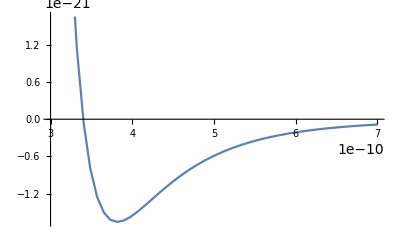

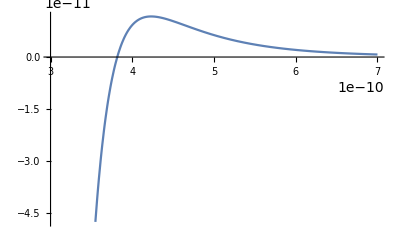

-Graphics-

```mathematica
T=120;
sigma=3.4*^-10;
kB=1.38064852*^-23;
epsilon=T*kB;
umass=1.660539040*^-27;
argonmass=umass*39.948;

min = 3*^-10;
max = 7*^-10;

4*ϵ*((σ/r)^12-(σ/r)^6)
D[-%,r]

Plot[4*epsilon*((sigma/r)^12-(sigma/r)^6),{r,min,max}]
Plot[24*epsilon*(sigma)^6*((r)^6-2*(sigma)^6)/(r)^13,{r,min,max}]
Plot[-24/r^2*epsilon*(2(sigma/r^12)-6(sigma/r^6)),{r,min,max}]

Manipulate[4*epsilon*((sigma/r)^12-(sigma/r)^6),{r,min,max}]
Manipulate[24*epsilon*(sigma)^6*((r)^6-2*(sigma)^6)/(r)^13,{r,min,max}]
```

```mathematica
scaleFactor=10^9;
initPositions= ReadList["~/phd-stuff/courses/astrid_sim/radialdistpos.txt",Number,RecordLists->True]*scaleFactor;
ListPointPlot3D[initPositions,BoxRatios->{1, 1, 1},AxesLabel->{"x","y","z"}]
```

-Graphics3D-

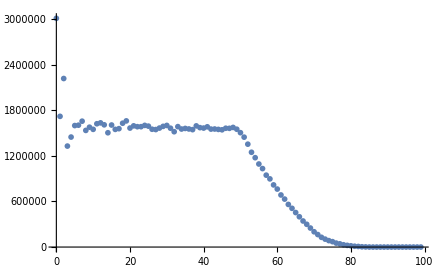

```mathematica
rdf= ReadList["~/phd-stuff/courses/astrid_sim/radialdistfunc.txt",Number,RecordLists->True];
ListPlot[rdf]
```

```mathematica
sigma=3.4*^-10;
boxlength=10.229*sigma
boxlength/5
Sqrt[3]*boxlength/2
a={boxlength/2,boxlength/2,boxlength/2};
b={0,0,0};
EuclideanDistance[a,b]
```

3.47786×10^-9

6.95572×10^-10

3.01192×10^-9

3.01192×10^-9